## Data from the Spray

This notebook contains data extracted from the plans for the Spray, including the waterline dwl and the section curve at station 2. We’ve included appropriate plot statements to get you started - notice that we have used AspectRatio -> Automatic which uses the same scale horizontally and vertically, which is appropriate for a geometric object. 

It’s important to note that we’ve already made some key decisions in defining and plotting the data in this way. Here are the key points:

To define the waterline dwl we look at the waterline curves in the middle figure and the data in the table on the left. We extract from the row of the table labelled dwl the coordinates of point that will capture the data and produce an approximation to the dwl waterline curve in the middle figure. We read the data from left to right, with the first point at station 1 and the last point at station 11. For example, we define the first entry in this row as the point with coordinates (3,-(1+1/12+6/96)). We use “3” as the x-coordinate for station 1, which implies that the origin of the x-axis lies at the front of the boat and is labeled “FP” on the plans - this stands for “forward perpendicular” in boat language. We use negative values for the y-coordinate so that the resulting approximation will “look” like the curves in the plan. We keep the measurements in feet so that 116 in the plans (1 foot, 1 inch, and 6-eighths of an inch) translates to 1+1/12+6/96.

To define the section curve at station 2 we look at the section curves in the bottom figure and the data in the table on the left and the table on the right. To produce a curve that “looks” like the curve in the plans, we treat the entries in the table on the left as the x-coordinates and the height above or below the dwl waterline as the y-coordinates. We treat the dwl waterline as the origin of the y-axis, so that points below it are negative and points above it are positive. We’ve also had to refer to the table on the right to determine the height of the points listed as sheer, which on a boat refers to the point at which the hull joins the deck. The sheer at station 2 is listed as 7 feet, 4 inches, and 6-eighths of an inch above the base, which is just 2 feet, 2 inches, and 6-eighths of an inch above the dwl waterline, which is what we are using as the origin of our y-axis.

{{3,-55/48},{6,-97/24},{9,-265/48},{12,-607/96},{15,-323/48},{18,-41/6},{21,-323/48},{24,-155/24},{27,-6},{30,-21/4},{33,-91/24}}

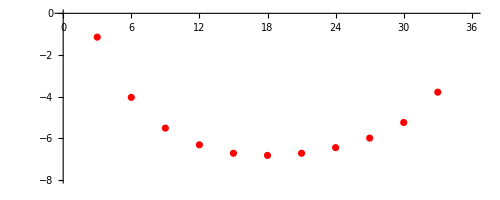

```mathematica
dwl = {{3,-(1+1/12+6/96)},{6,-(4+0/12+4/96)},{9,-(5+6/12+2/96)},{12,-(6+3/12+7/96)},{15,-(6+8/12+6/96)},{18,-(6+10/12+0/196)},{21,-(6+8/12+6/96)},{24,-(6+5/12+4/96)},{27,-(6+0/12+0/96)},{30,-(5+3/12+0/96)},{33,-(3+9/12+4/96)}}
ListPlot[dwl, PlotStyle->Red,PlotRange->{{0,36},{-8,0}},AspectRatio->Automatic]
```

```mathematica
Manipulate[Show[ListPlot[dwl, PlotStyle->Red,PlotRange->{{0,36},{-8,0}},AspectRatio->Automatic] ,Plot[g*(x-h)^2+k,{x,0,35},PlotRange->{{0,36},{-8,0}}]],{g,0,0.1,Appearance->"Labeled"},{h,15,25,Appearance->"Labeled"},{k,-8,-2,Appearance->"Labeled"}]
```

k+g (-h+x)^2

{{g,0.1},{h,25},{k,-4}}

{g→0.0191471,h→19.5645,k→-7.11765}

-7.11765+0.0191471 (-19.5645+x)^2

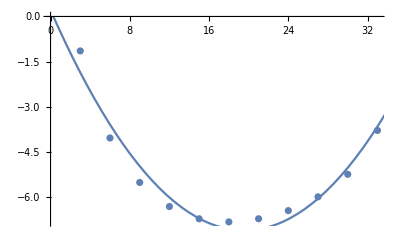

```mathematica
curve = g*(x-h)^2+k
params = {{g,0.1},{h,25}, {k,-4}}
bestparams = FindFit[dwl,curve,params,x]
bestcurve = curve/.bestparams
Show[ListPlot[dwl],Plot[bestcurve,{x,0,36},PlotRange->{{0,36},{-8,0}}]]
```

{{13/16,-2},{41/24,-3/2},{259/96,-1},{83/24,-1/2},{97/24,0},{35/8,1/2},{443/96,1},{115/24,3/2},{247/48,155/48}}

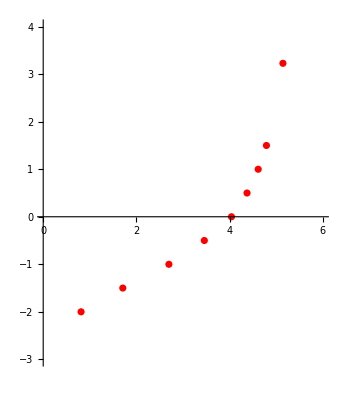

```mathematica
station2 = {{0+9/12+6/96,-24/12},{1+8/12+4/96,-18/12},{2+8/12+3/96,-12/12},{3+5/12+4/96,-6/12},{4+0/12+4/96,0/12},{4+4/12+4/96,6/12},{4+7/12+3/96,12/12},{4+9/12+4/96,18/12},{5+1/12+6/96,3+2/12+6/96}}
ListPlot[station2, PlotStyle->Red,PlotRange->{{0,6},{-3,4}},AspectRatio->Automatic]
```

```mathematica
Manipulate[Show[ListPlot[station2, PlotStyle->Red,PlotRange->{{0,6},{-3,4}},AspectRatio->Automatic] ,Plot[A*Exp[k*x]+b,{x,0,35},PlotRange->{{0,6},{-3,4}}]],{A,0,1,Appearance->"Labeled"},{k,0,1,Appearance->"Labeled"}, {b,-3,-1,Appearance->"Labeled"}]
```

b+A ⅇ^(k x)

{{A,0.206},{k,0.582},{b,-2.334}}

{A→0.0436673,k→0.912583,b→-1.76752}

-1.76752+0.0436673 ⅇ^(0.912583 x)

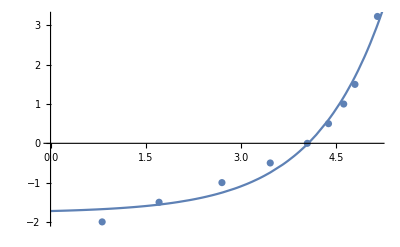

```mathematica
curve = A*Exp[k*x] +b
params = {{A,0.206}, {k,0.582}, {b, -2.334}}
bestparams = FindFit[station2,curve,params,x]
bestcurve = curve/.bestparams
Show[ListPlot[station2],Plot[bestcurve,{x,0,36},PlotRange->{{0,6},{-3,4}}]]
```

```mathematica
Manipulate[Show[ListPlot[station2, PlotStyle->Red,PlotRange->{{0,6},{-3,4}},AspectRatio->Automatic] ,Plot[A*x^n+b,{x,0,35},PlotRange->{{0,6},{-3,4}}]],{A,0,1,Appearance->"Labeled"},{n,1,2,Appearance->"Labeled"}, {b,-3,-1,Appearance->"Labeled"}]
```

b+A x^n

{{A,0.174},{n,1.914},{b,-2.218}}

{A→0.00304584,n→4.46005,b→-1.57854}

-1.57854+0.00304584 x^4.46005

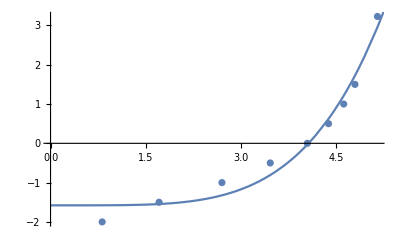

```mathematica
curve = A*x^n+b
params = {{A,0.174}, {n,1.914}, {b, -2.218}}
bestparams = FindFit[station2,curve,params,x]
bestcurve = curve/.bestparams
Show[ListPlot[station2],Plot[bestcurve,{x,0,36},PlotRange->{{0,6},{-3,4}}]]
```

The first set of data (dwl) fits pretty well with a parabolic function. I think a parabola is the ideal function for this set of data.
Due to a misunderstanding, I plotted the second set of data with both an exponential (e^x) and power (x^n) function. Surprisingly, both kinds of functions fit the data approximately equally well by just looking.